```mathematica
Needs["VariationalMethods`"];
ClearAll["Global`*"];
pars = {Subscript[m, 1]->1,Subscript[m, 2]->1.5,Subscript[l, 1]->1, Subscript[l, 2]->0.8, g->9.81};
```

```mathematica
T[t_]=1/2((Subscript[m, 1] Subscript[l, 1]^2)/3+(Subscript[m, 2] Subscript[l, 2]^2)/12+ Subscript[m, 2] Subscript[l, 1]^2)ϕ'[t]^2+1/2(Subscript[m, 2] Subscript[l, 2]^2)/12 θ'[t]^2
V[t_]=g(1/2 Subscript[m, 1] Subscript[l, 1] Sin[ϕ[t]] + Subscript[m, 2] Subscript[l, 1] Sin[ϕ[t]])
L[t_]=T[t]-V[t]
eqns={EulerEquations[L[t],ϕ[t],t]/.{0->F[t]},EulerEquations[L[t],θ[t],t]}
sys = NonlinearStateSpaceModel[eqns/.pars, {{ϕ[t],0}, {θ[t],π}}, {F[t]},{ϕ[t], θ[t]}, t]
```

1/24 l_2^2 m_2 θ'[t]^2+1/2 (1/3 l_1^2 m_1+l_1^2 m_2+1/12 l_2^2 m_2) ϕ'[t]^2

g (1/2 Sin[ϕ[t]] l_1 m_1+Sin[ϕ[t]] l_1 m_2)

-g (1/2 Sin[ϕ[t]] l_1 m_1+Sin[ϕ[t]] l_1 m_2)+1/24 l_2^2 m_2 θ'[t]^2+1/2 (1/3 l_1^2 m_1+l_1^2 m_2+1/12 l_2^2 m_2) ϕ'[t]^2

{-1/2 g Cos[ϕ[t]] l_1 (m_1+2 m_2)-1/12 (l_2^2 m_2+4 l_1^2 (m_1+3 m_2)) ϕ''[t]==F[t],-1/12 l_2^2 m_2 θ''[t]==0}

0.+1. x_2[t]0.-0.522648 (0.+19.62 Cos[x_1[t]]+F[t])0.+1. x_4[t]0.x_1[t]x_3[t]{x_1[t],0}x_2[t]{x_3[t],π}x_4[t] 4122NoneNoneFalseFalseFalse{F[t]}t

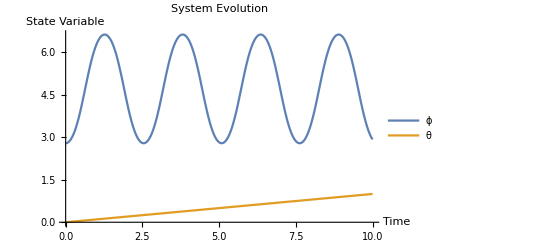

```mathematica
resp = OutputResponse[{sys, {160°,0,0,0.1}},0,{t,0,10}];
Plot[resp, {t,0,10}, PlotLegends->{"ϕ", "θ"}, PlotLabel-> "System Evolution", AxesLabel->{"Time", "State Variable"}]
```